```mathematica
data1 = Import["/net/home/f09/bajennissen/research/DAY197/tau_day_data/368nm.dat"]
data1hour=Drop[data1, None,1]
data2 = Import["/net/home/f09/bajennissen/research/DAY197/tau_day_data/412nm.dat"]
data2hour=Drop[data2,None,1]
data3 = Import["/net/home/f09/bajennissen/research/DAY197/tau_day_data/500nm.dat"]
data3hour=Drop[data3,None,1]
data4 = Import["/net/home/f09/bajennissen/research/DAY197/tau_day_data/610nm.dat"]
data4hour=Drop[data4,None,1]
data5 = Import["/net/home/f09/bajennissen/research/DAY197/tau_day_data/675nm.dat"]
data5hour=Drop[data5,None,1]
data6= Import["/net/home/f09/bajennissen/research/DAY197/tau_day_data/778nm.dat"]
data6hour=Drop[data6,None,1]
data7 = Import["/net/home/f09/bajennissen/research/DAY197/tau_day_data/862nm.dat"]
data7hour=Drop[data7,None,1]
```

{{197.357,8.56667,0.143662},{197.364,8.73333,0.141608},{197.384,9.21667,0.141238},{197.391,9.38333,0.153248},{197.398,9.55,0.150559},{197.406,9.75,0.198597},{197.413,9.91667,0.369748},{197.419,10.05,0.520551},{197.428,10.2667,0.811688},{197.435,10.45,1.12858},{197.441,10.5833,1.31109},{197.452,10.85,1.7346},{197.499,11.9833,0.311297},{197.51,12.2333,0.393667},{197.519,12.45,0.391238},{197.526,12.6333,0.373565},{197.533,12.8,0.361323},{197.544,13.05,0.313171},{197.551,13.2333,0.280884},{197.56,13.4333,0.271889},{197.565,13.5667,0.28737},{197.58,13.9167,0.273312},{197.599,14.3667,0.231095},{197.609,14.6167,0.249225},{197.616,14.7833,0.270727},{197.624,14.9667,0.262476}}

{{8.56667,0.143662},{8.73333,0.141608},{9.21667,0.141238},{9.38333,0.153248},{9.55,0.150559},{9.75,0.198597},{9.91667,0.369748},{10.05,0.520551},{10.2667,0.811688},{10.45,1.12858},{10.5833,1.31109},{10.85,1.7346},{11.9833,0.311297},{12.2333,0.393667},{12.45,0.391238},{12.6333,0.373565},{12.8,0.361323},{13.05,0.313171},{13.2333,0.280884},{13.4333,0.271889},{13.5667,0.28737},{13.9167,0.273312},{14.3667,0.231095},{14.6167,0.249225},{14.7833,0.270727},{14.9667,0.262476}}

{{197.357,8.56667,0.149248},{197.364,8.73333,0.156196},{197.384,9.21667,0.166425},{197.391,9.38333,0.168903},{197.398,9.55,0.16846},{197.406,9.75,0.209782},{197.413,9.91667,0.296867},{197.419,10.05,0.371434},{197.428,10.2667,0.492306},{197.435,10.45,0.616047},{197.441,10.5833,0.687064},{197.452,10.85,0.774677},{197.499,11.9833,0.266343},{197.51,12.2333,0.317225},{197.519,12.45,0.314281},{197.526,12.6333,0.304458},{197.533,12.8,0.302805},{197.544,13.05,0.269869},{197.551,13.2333,0.251124},{197.56,13.4333,0.240215},{197.565,13.5667,0.257707},{197.58,13.9167,0.240206},{197.599,14.3667,0.224207},{197.609,14.6167,0.210867},{197.616,14.7833,0.226505},{197.624,14.9667,0.226262}}

{{8.56667,0.149248},{8.73333,0.156196},{9.21667,0.166425},{9.38333,0.168903},{9.55,0.16846},{9.75,0.209782},{9.91667,0.296867},{10.05,0.371434},{10.2667,0.492306},{10.45,0.616047},{10.5833,0.687064},{10.85,0.774677},{11.9833,0.266343},{12.2333,0.317225},{12.45,0.314281},{12.6333,0.304458},{12.8,0.302805},{13.05,0.269869},{13.2333,0.251124},{13.4333,0.240215},{13.5667,0.257707},{13.9167,0.240206},{14.3667,0.224207},{14.6167,0.210867},{14.7833,0.226505},{14.9667,0.226262}}

{{197.357,8.56667,0.120696},{197.364,8.73333,0.124564},{197.384,9.21667,0.130064},{197.391,9.38333,0.137406},{197.398,9.55,0.134804},{197.406,9.75,0.154339},{197.413,9.91667,0.185243},{197.419,10.05,0.21052},{197.428,10.2667,0.255784},{197.435,10.45,0.29261},{197.441,10.5833,0.309464},{197.452,10.85,0.33866},{197.499,11.9833,0.165757},{197.51,12.2333,0.187214},{197.519,12.45,0.184134},{197.526,12.6333,0.18108},{197.533,12.8,0.178599},{197.544,13.05,0.166502},{197.551,13.2333,0.155149},{197.56,13.4333,0.153968},{197.565,13.5667,0.165285},{197.58,13.9167,0.152689},{197.599,14.3667,0.142794},{197.609,14.6167,0.135573},{197.616,14.7833,0.150529},{197.624,14.9667,0.14196}}

{{8.56667,0.120696},{8.73333,0.124564},{9.21667,0.130064},{9.38333,0.137406},{9.55,0.134804},{9.75,0.154339},{9.91667,0.185243},{10.05,0.21052},{10.2667,0.255784},{10.45,0.29261},{10.5833,0.309464},{10.85,0.33866},{11.9833,0.165757},{12.2333,0.187214},{12.45,0.184134},{12.6333,0.18108},{12.8,0.178599},{13.05,0.166502},{13.2333,0.155149},{13.4333,0.153968},{13.5667,0.165285},{13.9167,0.152689},{14.3667,0.142794},{14.6167,0.135573},{14.7833,0.150529},{14.9667,0.14196}}

{{197.357,8.56667,0.121256},{197.364,8.73333,0.122715},{197.384,9.21667,0.126107},{197.391,9.38333,0.127967},{197.398,9.55,0.129699},{197.406,9.75,0.145164},{197.413,9.91667,0.180116},{197.419,10.05,0.209232},{197.428,10.2667,0.258318},{197.435,10.45,0.292316},{197.441,10.5833,0.313753},{197.452,10.85,0.347164},{197.499,11.9833,0.163504},{197.51,12.2333,0.180611},{197.519,12.45,0.177537},{197.526,12.6333,0.176985},{197.533,12.8,0.173821},{197.544,13.05,0.15957},{197.551,13.2333,0.151799},{197.56,13.4333,0.150179},{197.565,13.5667,0.152572},{197.58,13.9167,0.147117},{197.599,14.3667,0.135744},{197.609,14.6167,0.134589},{197.616,14.7833,0.141405},{197.624,14.9667,0.133598}}

{{8.56667,0.121256},{8.73333,0.122715},{9.21667,0.126107},{9.38333,0.127967},{9.55,0.129699},{9.75,0.145164},{9.91667,0.180116},{10.05,0.209232},{10.2667,0.258318},{10.45,0.292316},{10.5833,0.313753},{10.85,0.347164},{11.9833,0.163504},{12.2333,0.180611},{12.45,0.177537},{12.6333,0.176985},{12.8,0.173821},{13.05,0.15957},{13.2333,0.151799},{13.4333,0.150179},{13.5667,0.152572},{13.9167,0.147117},{14.3667,0.135744},{14.6167,0.134589},{14.7833,0.141405},{14.9667,0.133598}}

{{197.357,8.56667,0.0945038},{197.364,8.73333,0.099398},{197.384,9.21667,0.10359},{197.391,9.38333,0.10141},{197.398,9.55,0.103359},{197.406,9.75,0.13019},{197.413,9.91667,0.178839},{197.419,10.05,0.224206},{197.428,10.2667,0.306429},{197.435,10.45,0.364848},{197.441,10.5833,0.39847},{197.452,10.85,0.454633},{197.499,11.9833,0.173348},{197.51,12.2333,0.195303},{197.519,12.45,0.194057},{197.526,12.6333,0.18712},{197.533,12.8,0.182725},{197.544,13.05,0.175664},{197.551,13.2333,0.160885},{197.56,13.4333,0.155247},{197.565,13.5667,0.159066},{197.58,13.9167,0.148914},{197.599,14.3667,0.13815},{197.609,14.6167,0.135596},{197.616,14.7833,0.140731},{197.624,14.9667,0.129792}}

{{8.56667,0.0945038},{8.73333,0.099398},{9.21667,0.10359},{9.38333,0.10141},{9.55,0.103359},{9.75,0.13019},{9.91667,0.178839},{10.05,0.224206},{10.2667,0.306429},{10.45,0.364848},{10.5833,0.39847},{10.85,0.454633},{11.9833,0.173348},{12.2333,0.195303},{12.45,0.194057},{12.6333,0.18712},{12.8,0.182725},{13.05,0.175664},{13.2333,0.160885},{13.4333,0.155247},{13.5667,0.159066},{13.9167,0.148914},{14.3667,0.13815},{14.6167,0.135596},{14.7833,0.140731},{14.9667,0.129792}}

{{197.357,8.56667,0.105515},{197.364,8.73333,0.120642},{197.384,9.21667,0.122118},{197.391,9.38333,0.126504},{197.398,9.55,0.132829},{197.406,9.75,0.16313},{197.413,9.91667,0.288932},{197.419,10.05,0.400455},{197.428,10.2667,0.647922},{197.435,10.45,0.844631},{197.441,10.5833,0.995267},{197.452,10.85,1.23526},{197.499,11.9833,0.297823},{197.51,12.2333,0.36177},{197.519,12.45,0.38082},{197.526,12.6333,0.357363},{197.533,12.8,0.344277},{197.544,13.05,0.317737},{197.551,13.2333,0.288409},{197.56,13.4333,0.27578},{197.565,13.5667,0.264213},{197.58,13.9167,0.260518},{197.599,14.3667,0.232655},{197.609,14.6167,0.227484},{197.616,14.7833,0.229949},{197.624,14.9667,0.225825}}

{{8.56667,0.105515},{8.73333,0.120642},{9.21667,0.122118},{9.38333,0.126504},{9.55,0.132829},{9.75,0.16313},{9.91667,0.288932},{10.05,0.400455},{10.2667,0.647922},{10.45,0.844631},{10.5833,0.995267},{10.85,1.23526},{11.9833,0.297823},{12.2333,0.36177},{12.45,0.38082},{12.6333,0.357363},{12.8,0.344277},{13.05,0.317737},{13.2333,0.288409},{13.4333,0.27578},{13.5667,0.264213},{13.9167,0.260518},{14.3667,0.232655},{14.6167,0.227484},{14.7833,0.229949},{14.9667,0.225825}}

{{197.357,8.56667,0.088851},{197.364,8.73333,0.0973347},{197.384,9.21667,0.0885856},{197.391,9.38333,0.113607},{197.398,9.55,0.118454},{197.406,9.75,0.177249},{197.413,9.91667,0.426577},{197.419,10.05,0.688437},{197.428,10.2667,1.61499},{197.435,10.45,inf},{197.441,10.5833,inf},{197.452,10.85,inf},{197.499,11.9833,0.45506},{197.51,12.2333,0.615933},{197.519,12.45,0.602461},{197.526,12.6333,0.584236},{197.533,12.8,0.570245},{197.544,13.05,0.488616},{197.551,13.2333,0.447311},{197.56,13.4333,0.412418},{197.565,13.5667,0.377085},{197.58,13.9167,0.372677},{197.599,14.3667,0.336298},{197.609,14.6167,0.339596},{197.616,14.7833,0.319418},{197.624,14.9667,0.321423}}

{{8.56667,0.088851},{8.73333,0.0973347},{9.21667,0.0885856},{9.38333,0.113607},{9.55,0.118454},{9.75,0.177249},{9.91667,0.426577},{10.05,0.688437},{10.2667,1.61499},{10.45,inf},{10.5833,inf},{10.85,inf},{11.9833,0.45506},{12.2333,0.615933},{12.45,0.602461},{12.6333,0.584236},{12.8,0.570245},{13.05,0.488616},{13.2333,0.447311},{13.4333,0.412418},{13.5667,0.377085},{13.9167,0.372677},{14.3667,0.336298},{14.6167,0.339596},{14.7833,0.319418},{14.9667,0.321423}}

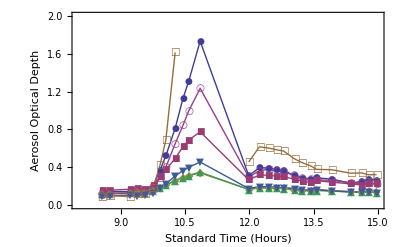

```mathematica
<<PlotLegends`
DataPlot=ListPlot[{data1hour,data2hour,data3hour,data4hour,data5hour,data6hour,data7hour}, PlotStyle->PointSize[0.02],PlotMarkers->Automatic,Joined->True,PlotLegend->{"368nm","412nm","500nm","610nm","675nm","778nm","862nm"},LegendPosition->{1.1,-0.4}, LegendSize->{0.5,0.75},PlotRange->{{8,15},{0,2}},Frame->True, AxesOrigin-> {8,0},LegendShadow->None,FrameLabel->{{"Aerosol Optical Depth",""},{"Standard Time (Hours)","Day 197 July 16th, 2010"}}]
```